```mathematica
【通用模型的数值解】
```

```mathematica
w=((1+α) (c+2 c α+a (α+θ))-(1+2 α) (1+α-μ α) Subscript[c, r])/(2 (1+α) (1+2 α))
```

```mathematica
pd=(2 (1+α)^2 (c+2 c α+a (1+α-θ)) (-2+Subscript[τ, r])+2 (1+α)^2 (1+2 α) Subscript[c, d] (-2+Subscript[τ, r])+Subscript[τ, m] ((1+α) (c α (1+2 α)+a (4+α (8+α)))-a (4+3 α (3+α)) θ+α (1+2 α) (1+α-α μ) Subscript[c, r]-2 a (1+2 α) (1+α-θ) Subscript[τ, r]))/(2 (1+2 α) (2 (1+α)^2 (-2+Subscript[τ, r])+Subscript[τ, m] (2+α (4+α)-(1+2 α) Subscript[τ, r])))
```

```mathematica
pr=(-2 (1+α) (2 a α (1+α)+c (1+2 α)^2+a (3+4 α) θ)-(1+α) (1+2 α) (-1+α (-1+μ)) Subscript[c, r] (-2+Subscript[τ, m])+(c (1+α)^2 (1+2 α)+a (3+α (6+α)) (α+θ)) Subscript[τ, m]+2 α (1+α) (1+2 α) Subscript[c, d] (-1+Subscript[τ, r])+2 ((1+α) (α (a+c+a α+2 c α)+a (2+3 α) θ)-a (1+2 α) (α+θ) Subscript[τ, m]) Subscript[τ, r])/(2 (1+2 α) (2 (1+α)^2 (-2+Subscript[τ, r])+Subscript[τ, m] (2+α (4+α)-(1+2 α) Subscript[τ, r])))
```

```mathematica
【看制造商的决策和搭便车的关系】
```

```mathematica
a=40
c=2
Subscript[c, r]=0.5
Subscript[c, d] =0.5
θ=0.5
α=0.5
Subscript[τ, r]=0.5
Subscript[τ, m]=0.5
```

40

2

0.5

0.5

0.5

«3 more identical outputs»

```mathematica
Plot【f，{x，0，3}，frame->True，GridLines->Automatic，PlotStyle->{Thickness[0.01]}，AxesLabel->{"X","y"}，Background->RGBColor[0,1,1]】
```

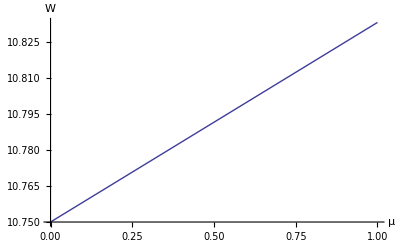

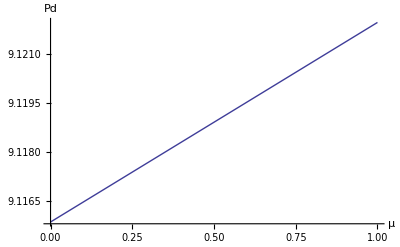

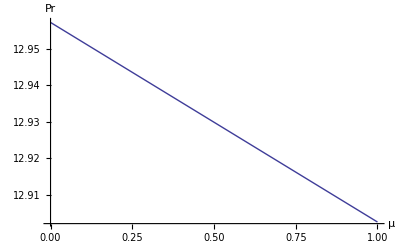

```mathematica
p1=Plot[w,{μ,0,1},AxesLabel->{μ,W}]
p2=Plot[pd,{μ,0,1},AxesLabel->{μ,Pd}]
p3=Plot[pr,{μ,0,1},AxesLabel->{μ,Pr}]
```

Show[GraphicsGrid[-Graphics-,-Graphics-,-Graphics-]]

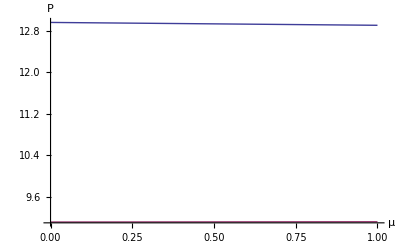

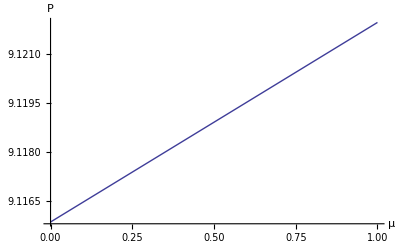

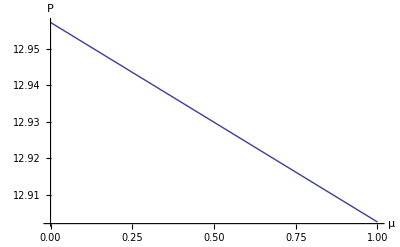

```mathematica
Show[GraphicsGrid[p1,p2,p3]]
```

```mathematica
Plot3D[w,{μ,0,1}]
```

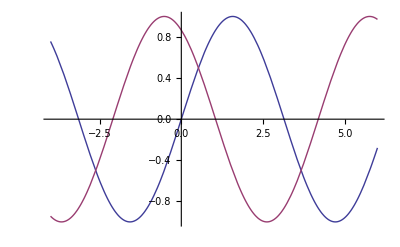

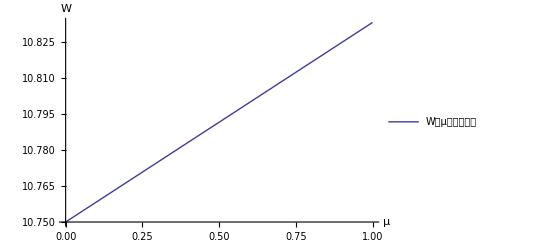

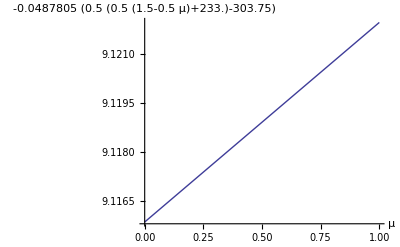

```mathematica
Plot[{Sin[x],Cos[x+Pi/6]},{x,-4,6}]
```

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2,2},ColorFunction->(ColorData["TemperatureMap",#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[(4a b*b +6a*a*b+b*b*b)/(6a*a*a+4 a*b*b+6 *a*a*b+b*b*b),{a,0,4},{b,0,4},ColorFunction->(ColorData["TemperatureMap",#3]&
```

-Graphics3D-